# 钢管订购和运输计划的优化作业

代码编写：杨永康      论文编写：杨永康     作者：杨永康        队伍：19队

## 第一题题目

### 问题背景：

要铺设一条输送天然气的主管道A1->A2->...->A15,能生产这种钢管的厂家一共有：S1，S2，...,S7，厂家与管道之间的交通网络已知，假设沿着管道，或者有就公路，或者建有施工公路。

(1)请制定一个主管道钢管的订购和运输计划， 使总费用最小(给出总费用)

### 需要解决的问题:

计算第一问中的求单位钢管从钢厂运到运输点的最小费用Aij（做成一个表格）

### 解决思路：

方法:将图转换为一个以单位钢管的运输费用为权的赋权图，再求最短路的权。
由于运输过程中既有铁路，也有公路。
铁路的运费还是分段函数，与全程运输总距离有 关 ;各路运费确是线性函数。
可考虑将铁路与公路分开考虑。

### 构造铁路网，并计算Si 到各节点 的最小费用：

#### 铁路的构建

首先将厂家的地址在图上用S1, S2, ... S7；其中序号1～17表示铁路点，如下图所示

-Graphics-

#### Wolfram语言编写铁路图

```mathematica
RailroadMap={1<->3,3<->2,3<->4,4<->5,5<->s2,5<->s1,s1<->7,7<->8,8<->9,5<->10,10<->s3,10<->11,11<->12,12<->s4,12<->13,12<->14,14<->s5,13<->15,13<->16,16<->17,17<->s6,17<->18,18<->s7};
```

```mathematica
EdgeWeightList={450,80,1150,1100,1200,202,20,195,306,720,690,520,170,690,160,88,462,70,320,160,70,290,30};
```

```mathematica
vertexlist={1,2,4,9,8,7,s1,5,10,11,14,15,16,s6,17,18,s7};
```

```mathematica
start={s1,s2,s3,s4,s5,s6,s7};
```

```mathematica
end=ToExpression["A"<>ToString[#]&/@Range[2,15]];
```

```mathematica
graph=Graph[RailroadMap,VertexLabels->Automatic,EdgeWeight->EdgeWeightList,VertexSize->0.4,VertexStyle->(Rule[#,Red]&/@start)~Join~(Rule[#,Yellow]&/@vertexlist)];
```

#### 铁路网图形的绘制

红色点代表钢厂，黄色点代表需要到达的铁路站点。

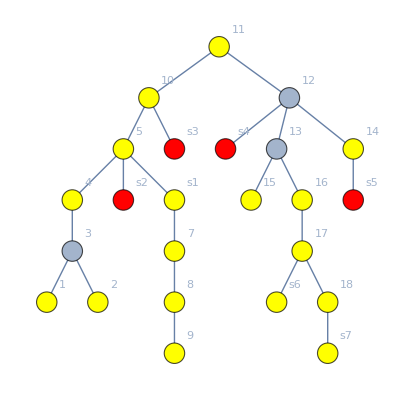

```mathematica
graph
```

#### Si 到各节点 之间的最短路程

利用Wolfram语言编写代码

```mathematica
graphdistance=Table[GraphDistance[graph,s,e],{s,start},{e,vertexlist}];
```

#### Si 到各节点 之间的最短路程的表格形式

```mathematica
Dataset@Table[<|"EndVertex"->vertexlist[[i]]|>~Join~AssociationThread["s"<>ToString[#]&/@Range[7],graphdistance[[#]][[i]]&/@Range[7]],{i,1,17}]
```

Dataset[<>]

#### 铁路路程计费函数的构建

-Graphics-

```mathematica
CostPrice=Function[{x},Piecewise[{{20,0<x≤300},{23,x≤350&&x≥301},{26,x≥351&&x≤400},{29,x≥401&&x≤450},{32,x≥451&&x≤500},{37,x≥501&&x≤600},{44,x≥601&&x≤700},{50,x≥701&&x≤800},{55,x≥801&&x≤900},{60,x≥901&&x≤1000},{60+Ceiling[(x-1000)/100]*5,x≥1000},{0,True}}]];
```

#### Si 到各节点 之间的最短路程转换成最少费用

```mathematica
CostPriceList=(CostPrice@#&/@(Flatten@graphdistance))~Partition~17;
```

#### Si 到各节点 之间的最少费用表格

```mathematica
Dataset@Table[<|"EndVertex"->vertexlist[[i]]|>~Join~AssociationThread["s"<>ToString[#]&/@Range[7],CostPriceList[[#]][[i]]&/@Range[7]],{i,1,17}]
```

Dataset[<>]

### 合并铁路和公路图得以费用为权的交通网络图

#### Wolfram语言编写铁路和公路图

```mathematica
remain=MapThread[UndirectedEdge,{vertexlist[[;;6]],end[[;;6]]}]~Join~(MapThread[UndirectedEdge,{vertexlist[[8;;14]],end[[7;;13]]}]~Join~{s1<->A7,17<->A14,18<->A15,S7<->15});
```

```mathematica
FinalGraphRule=Flatten@Table[i<->j,{i,ToExpression["s"<>ToString[#]&/@Range[7]]},{j,vertexlist}]~Join~remain;
```

```mathematica
edgeweightlist=Flatten@CostPriceList~Join~(0.1*{3,2,600,10,5,10,12,42,70,10,10,62,110,31,30,20,20});
```

```mathematica
finalgraph=Graph[FinalGraphRule,VertexLabels->Automatic,EdgeWeight->edgeweightlist,VertexStyle->(Rule[#,Red]&/@start)~Join~(Rule[#,Yellow]&/@end),VertexSize->0.5];
```

#### 铁路和公路图可视化

红色点代表钢厂，黄色点代表需要到达的公路站点。

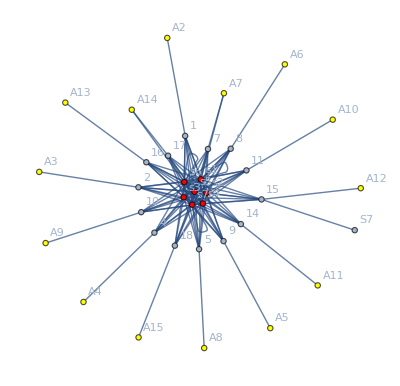

```mathematica
finalgraph
```

#### 计算S1到结点Ai的最小费用

```mathematica
TotalPriceList=Table[GraphDistance[finalgraph,s,e],{s,start},{e,end}]+{160,155,155,160,155,150,160};
```

#### S1到结点Ai的最小费用表格

```mathematica
Dataset@Table[<|"EndVertex"->end[[i]]|>~Join~AssociationThread["s"<>ToString[#]&/@Range[7],TotalPriceList[[#]][[i]]&/@Range[7]],{i,1,14}]
```

Dataset[<>]

## 第三问解答

### 需要解决的题目:

-Graphics-

### 解决思路：

参照第一问，先解决单位钢管从钢厂运到运输点的最小费用Aij，然后写出规划函数求出解决方案。

### 构造铁路网，并计算Si 到各节点 的最小费用：

#### 铁路的构建

首先将厂家的地址在图上用S1, S2, ... S7；其中序号1～12表示铁路点，如下图所示

#### Wolfram语言编写铁路图

```mathematica
RailroadMap1={1<->2,2<->3,2<->4,4<->5,5<->s2,5<->s1,s1<->6,6<->7,7<->8,5<->A16,A16<->s3,A16<->9,9<->10,10<->s4,10<->A17,A17<->s5,10<->A18,A18<->A19,A18<->A20,A20<->11,11<->s6,11<->12,12<->s7};
```

```mathematica
EdgeWeightList1={450,80,1150,1100,1200,202,20,195,306,720,690,520,170,690,88,462,160,70,320,160,70,290,3};
```

```mathematica
vertexlist1={1,3,4,6,7,8,s1,5,A16,9,10,A17,A18,A19,A20,11,s6,12,s7};
```

```mathematica
end1=Delete[ToExpression["A"<>ToString[#]&/@Range[21]],{{1},{9},{11}}];
```

#### 铁路网图形的绘制

红色点代表钢厂，黄色点代表需要到达的铁路站点。

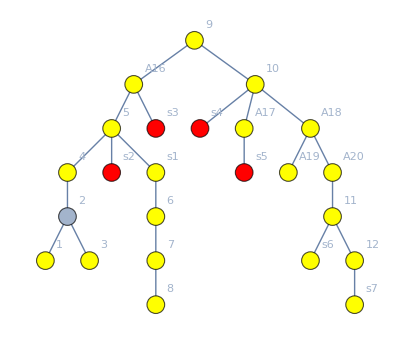

```mathematica
graph1=Graph[RailroadMap1,VertexLabels->Automatic,EdgeWeight->EdgeWeightList1,VertexStyle->(Rule[#,Red]&/@start)~Join~(Rule[#,Yellow]&/@vertexlist1),VertexSize->0.4]
```

#### Si 到各节点 之间的最短路程

利用Wolfram语言编写代码

```mathematica
graphdistance1=Table[GraphDistance[graph1,s,e],{s,start},{e,vertexlist1}];
```

#### Si 到各节点 之间的最短路程的表格形式

```mathematica
Dataset@Table[<|"EndVertex"->vertexlist1[[i]]|>~Join~AssociationThread["s"<>ToString[#]&/@Range[7],graphdistance1[[#]][[i]]&/@Range[7]],{i,1,19}]
```

Dataset[<>]

#### Si 到各节点 之间的最短路程转换成最少费用

```mathematica
CostPriceList1=(CostPrice@#&/@(Flatten@graphdistance1))~Partition~19;
```

#### Si 到各节点 之间的最少费用表格

```mathematica
Dataset@Table[<|"EndVertex"->vertexlist1[[i]]|>~Join~AssociationThread["s"<>ToString[#]&/@Range[7],CostPriceList1[[#]][[i]]&/@Range[7]],{i,1,19}]
```

Dataset[<>]

### 合并铁路和公路图得以费用为权的交通网络图

#### Wolfram语言编写铁路和公路图

```mathematica
remain1={1<->A2,3<->A3,4<->A4,8<->A5,7<->A6,6<->A7,s1<->A7,5<->A8,9<->A10,A19<->A12,A20<->A13,A21<->A14,11<->A14,12<->A15,s7<->A15,s6<->A21};
```

```mathematica
FinalGraphRule1=Flatten@Table[i<->j,{i,ToExpression["s"<>ToString[#]&/@Range[7]]},{j,vertexlist1}]~Join~remain1;
```

```mathematica
edgeweightlist1=Flatten@CostPriceList1~Join~(0.1*{3,2,600,10,5,10,31,12,70,10,62,110,30,20,20,0});
```

```mathematica
finalgraph1=Graph[FinalGraphRule1,EdgeWeight->edgeweightlist1,VertexLabels->Automatic,VertexStyle->(Rule[#,Red]&/@start)~Join~(Rule[#,Yellow]&/@end1),VertexSize->0.4];
```

#### 铁路和公路图可视化

红色点代表钢厂，黄色点代表需要到达的公路站点。

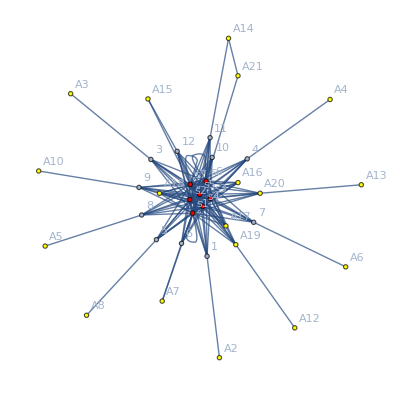

```mathematica
finalgraph1
```

#### 计算S1到结点Ai的最小费用

```mathematica
TotalPriceList1=Table[GraphDistance[finalgraph1,s,e],{s,start},{e,end1}]+{160,155,155,160,155,150,160};
```

#### 计算S1到结点Ai的最小费用表格

```mathematica
Dataset@Table[<|"EndVertex"->end1[[i]]|>~Join~AssociationThread["s"<>ToString[#]&/@Range[7],TotalPriceList1[[#]][[i]]&/@Range[7]],{i,1,18}]
```

Dataset[<>]

### 目标函数和规划函数的构建

#### 优化模型及符号介绍

-Graphics-

关于y_j的定义，我们定义优化模型，由于A9和A11所处的特殊位置，意思是把A8和A10之间，A10和A11之间看成一整段，忽略掉A9和A11，A16-A19，A17-A11道路全由到达A16和A17的管道铺设。对应的 y_j进行调整。

目标函数

-Graphics-

规划条件

-Graphics-

#### 目标函数和规划函数表达式

```mathematica
(*目标函数*)
```

```mathematica
function={Total@Flatten@Table[A[i,j]*x[i,j],{i,Range@7},{j,Range@18}]+Total@Table[(y[j]*(y[j]+1))/20+((d[j]-y[j])*(d[j]+1-y[j]))/20,{j,Range@12~Join~Range[15,18]}]+95.8};
```

```mathematica
(*约束条件*)
```

```mathematica
cons1=Table[Sum[x[i,j],{j,1,18}]≤s[i],{i,Range@7}];
```

```mathematica
cons2=Table[0<=y[j]≤d[j],{j,Range[2,12]~Join~Range[15,18]}];
```

```mathematica
cons3=Table[d[j]-y[j]+y[j+1]==Sum[x[i,j],{i,1,7}],{j,Range[1,12]}]~Join~{y[14]+y[15]+y[16]==Sum[x[i,14],{i,1,7}],d[16]-y[16]+y[17]==Sum[x[i,16],{i,1,7}],d[15]-y[15]==Sum[x[i,15],{i,1,7}],d[17]-y[17]+y[18]==Sum[x[i,17],{i,1,7}],d[18]-y[18]==Sum[x[i,18],{i,1,7}],Sum[x[i,13],{i,1,7}]==42};
```

```mathematica
cons4=Flatten@Table[x[i,j]≥0,{i,Range@7},{j,Range@18}];
```

```mathematica
(*变量*)
```

```mathematica
var=Flatten@Table[x[i,j],{i,Range@7},{j,Range@18}]~Join~Table[y[i],{i,Range[2,12]~Join~Range[15,18]}];
```

### 非线性规划的全局最优化求解

```mathematica
result=Block[{A=TotalPriceList1[[#1,#2]]&,s={800,800,1000,2000,2000,2000,3000}[[#]]&,d={104,301,750,606,194,205,201,1160,520,210,420,500,0,0,130,190,260,100}[[#]]&},NMinimize[Join[function,cons1,cons2,cons4,cons3,{Sum[x[7,j],{j,1,18}]==0}]/.{y[1]->0,y[14]->10,y[13]->0},var]];
```

### 具体计划购运表

```mathematica
MethodList=Partition[Values[result[[2]][[;;7*18]]],18]/.{x_/;Abs[x]≤0.001:>0};
```

```mathematica
totalsum=Total/@MethodList;
```

```mathematica
totalsum1=Total/@(Transpose@MethodList);
```

```mathematica
Dataset[Table[<|"EndVertex"->end1[[i]]|>~Join~AssociationThread["s"<>ToString[#]&/@Range[7],MethodList[[#]][[i]]&/@Range[7]]~Join~<|"Sum"->totalsum1[[i]]|>,{i,1,18}]~Join~{<|"EndVertex"->"Sum"|>~Join~AssociationThread["s"<>ToString[#]&/@Range[7],totalsum[[#]]&/@Range[7]]}]
```

Dataset[<>]

### 最少费用

```mathematica
result[[1]]
```

1.44547×10^6

该模型下所需最低费用144.547万